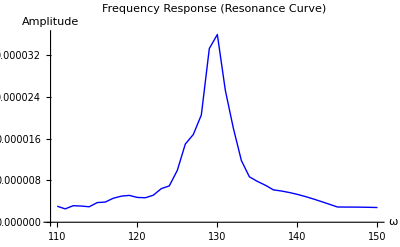

```mathematica
(*Define parameters*)
m=30; (*mass*)
k=504000; (*spring constant*)
mu=2; (*coefficient of friction*)
F0=0.3; (*driving force amplitude*)

(*Range of driving frequencies*)
omegaRange=Range[110,150,1];

(*Function to solve the system for a given driving frequency*)
solveForOmega[omega_]:=Module[{eq1,sol},eq1=m*x''[t]==-k*x[t]-mu*m*x'[t]+F0*Cos[omega*t];
sol=NDSolve[{eq1,x[0]==0,x'[0]==0},{x},{t,0,100}];
(*Extract the amplitude of the response*)Max[x[t]/. sol/. t->Range[0,100,0.1]]]

(*Calculate the amplitude for each driving frequency*)
amplitudes=ParallelMap[solveForOmega,omegaRange];

(*Plot the resonance curve*)
ListLinePlot[Transpose[{omegaRange,amplitudes}],PlotRange->All,PlotLabel->"Frequency Response (Resonance Curve)",AxesLabel->{"ω","Amplitude"},PlotStyle->{Blue,Thick}]
```